# Reproduzir exemplo 1 da tese de João Clávio (p. 401)

## Setup

```mathematica
Clear["Global`*"]
<<"C:\\Users\\pedro\\Documents\\Estudos\\UFRJ\\campos e ondas\\aplicacaoCamposOndas\\EletrodosFinitos.m"
```

```mathematica
μ0=4 10^-7 Pi;
ϵ0=8.8549 10^-12;
ω=2 Pi 10^-12;
raio=7 10^-3;
μcabo=μ0;
σcabo=5.65 10^7;
zinterno=1/(2 Pi raio) Sqrt[I μcabo ω/σcabo];
σ0=1 10^-3;
Δi=11.71 10^-3;
α=0.706;
sjweSolo=σ0+Δi (ω/(2 10^6 Pi))^α (I + 1/Tan[Pi/2 + α]); (*p. 213*)
sjweAr=I ω ϵ0;
R=(sjweSolo - sjweAr)/(sjweSolo + sjweAr);
γ=Sqrt[I ω μ0 sjweSolo];
```

## Eletrodos e Imagens

```mathematica
nodes={
{0.,0.,-0.5},
{6.,0.,-0.5},
{-6.,0.,-0.5},
{0.,6.,-0.5},
{0.,-6.,-0.5},
{0.,0.,-3.5},
{6.,0.,-3.5},
{-6.,0.,-3.5},
{0.,6.,-3.5},
{0.,-6.,-3.5}
};
correntesInjetadas=Table[0,nodes//Length];
correntesInjetadas[[1]]=1.0;
```

```mathematica
eletrodosHorizontais={
{nodes[[1]],nodes[[2]],raio,zinterno},
{nodes[[1]],nodes[[3]],raio,zinterno},
{nodes[[1]],nodes[[4]],raio,zinterno},
{nodes[[1]],nodes[[5]],raio,zinterno}
};
eletrodosVerticais={
{nodes[[1]],nodes[[6]],raio,zinterno},
{nodes[[2]],nodes[[7]],raio,zinterno},
{nodes[[3]],nodes[[8]],raio,zinterno},
{nodes[[4]],nodes[[9]],raio,zinterno},
{nodes[[5]],nodes[[10]],raio,zinterno}
};
eletrodos=Join[eletrodosHorizontais, eletrodosVerticais];
```

```mathematica
numEletrodos=Length[eletrodos];
pi=Table[eletrodos[[i,1]],{i,numEletrodos}];
pf=Table[eletrodos[[i,2]],{i,numEletrodos}];
linhas=Table[Line[{pi[[i]],pf[[i]]}],{i,numEletrodos}];
plot1=Graphics3D[linhas,Boxed->True];
plot2=ListPointPlot3D[nodes,PlotStyle->{PointSize[0.02],Black}];
malha=Show[plot1,plot2,Axes->False]
```

-Graphics3D-

#### Imagens

```mathematica
nodesimagens={
{0.,0.,0.5},
{6.,0.,0.5},
{-6.,0.,0.5},
{0.,6.,0.5},
{0.,-6.,0.5},
{0.,0.,3.5},
{6.,0.,3.5},
{-6.,0.,3.5},
{0.,6.,3.5},
{0.,-6.,3.5}
};
```

```mathematica
imagensHorizontais={
{nodesimagens[[1]],nodesimagens[[2]],raio,zinterno},
{nodesimagens[[1]],nodesimagens[[3]],raio,zinterno},
{nodesimagens[[1]],nodesimagens[[4]],raio,zinterno},
{nodesimagens[[1]],nodesimagens[[5]],raio,zinterno}
};
imagensVerticais={
{nodesimagens[[1]],nodesimagens[[6]],raio,zinterno},
{nodesimagens[[2]],nodesimagens[[7]],raio,zinterno},
{nodesimagens[[3]],nodesimagens[[8]],raio,zinterno},
{nodesimagens[[4]],nodesimagens[[9]],raio,zinterno},
{nodesimagens[[5]],nodesimagens[[10]],raio,zinterno}
};
imagens=Join[imagensHorizontais, imagensVerticais];
```

## Impedância

```mathematica
{zt, zl} = ImpedanciaEletrodos[eletrodos,γ,sjweSolo,μ0,ω,False];//AbsoluteTiming
```

{0.190632,Null}

### Efeito das imagens

```mathematica
{zt, zl} = IncluirImagensImpedancia[zt,zl,eletrodos,imagens,γ,sjweSolo,μ0,ω,R,False];
```

## Distribuição de potencial no solo

```mathematica
noinjecao=1;
correntesInjetadas=Table[0,Length[nodes]];
correntesInjetadas[[noinjecao]]=1;
nodes[[noinjecao]]
```

{0.,0.,-0.5}

```mathematica
{u, it, il} = ResolverEletrodos[eletrodos,zt,zl,correntesInjetadas,nodes];
```

Pontos nos quais calcular o potencial

```mathematica
range=Range[-12.,12,0.5];
{xx,yy}=meshgrid[range,range];
pontos2d=Flatten[{xx,yy},{2,3}];
```

```mathematica
(*https://mathematica.stackexchange.com/questions/3665/can-2d-and-3d-plots-be-combined-so-that-the-2d-plot-is-the-bottom-surface-of-the*)
Make3d[plot_,height_,opacity_]:=Module[{newplot},newplot=First@Graphics[plot];
newplot=N@newplot/.{x_?AtomQ,y_?AtomQ}:>{x,y,height};
newplot/.GraphicsComplex[xx__]:>{Opacity[opacity],GraphicsComplex[xx]}]
```

```mathematica
Show[{malha,Graphics3D[Make3d[ListPlot[pontos2d],0,1]]},Axes->False,ImageSize->Medium,Boxed->True,ViewPoint->Above]
```

-Graphics3D-

```mathematica
pot=ParallelTable[
Block[{u},
u=CalcularPotencial[Join[p,{0}],eletrodos,it,γ,sjweSolo,1];
u+=CalcularPotencial[Join[p,{0}],imagens,it,γ,sjweSolo,R];
Abs[u]
] 
,{p,pontos2d}
];//AbsoluteTiming
```

{1.35089,Null}

```mathematica
pts=Table[{pontos2d[[i,1]],pontos2d[[i,2]],pot[[i]]},{i,pontos2d//Length}];
```

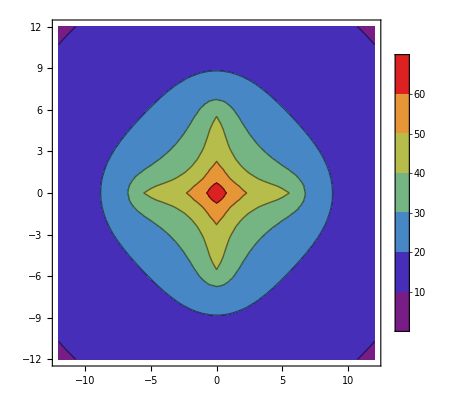

```mathematica
plotPotencial=ListContourPlot[pts,PlotLegends->Automatic,ColorFunction->"Rainbow",AspectRatio->Automatic]
```

## Campos Elétricos

### Campo elétrico induzido OverVector[E_c]

#### Por gradiente do potencial

```mathematica
(*gradiente do potencial*)
Clear[x,y];
fu=Interpolation[Transpose@{pontos2d,pot}];
dfu=Grad[fu[x,y],{x,y}];
campoEc[xx_,yy_]:=-dfu/.{x->xx,y->yy};
```

```mathematica
ec=Table[{p,campoEc[p[[1]],p[[2]]]},{p,pontos2d}];
```

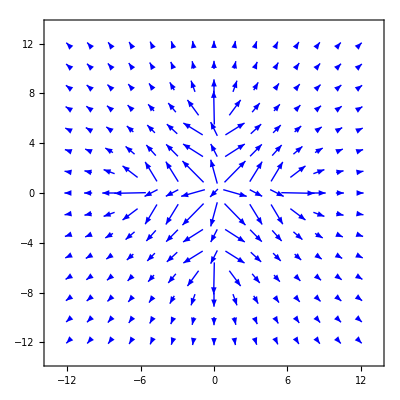

```mathematica
Show[ListVectorPlot[ec,VectorStyle->Blue,AspectRatio->Automatic,VectorScale->Medium]]
```

## Tensão de passo

```mathematica
Potencial[p_]:=Block[{u},
u=CalcularPotencial[p,eletrodos,it,γ,sjweSolo,1];
u+=CalcularPotencial[p,imagens,it,γ,sjweSolo,R];
u
];
CalcularTensaoPasso[ponto_]:=
Block[{pi,p1,p2,p3,p4,tensao1,tensao2,tensao3,tensao4,pot},
pi=Join[ponto,{0}];
p1=pi+{Sqrt[2]/2,Sqrt[2]/2,0};
p2=pi+{-Sqrt[2]/2,Sqrt[2]/2,0};
p3=pi+{-Sqrt[2]/2,-Sqrt[2]/2,0};
p4=pi+{Sqrt[2]/2,-Sqrt[2]/2,0};
pot=Potencial[pi];
tensao1=pot-Potencial[p1];
tensao2=pot-Potencial[p2];
tensao3=pot-Potencial[p3];
tensao4=pot-Potencial[p4];
Max[Abs@{tensao1,tensao2,tensao3,tensao4}]
]
```

```mathematica
tensaoPasso=ParallelTable[
CalcularTensaoPasso[p]
,{p,pontos2d}
];//AbsoluteTiming
```

{6.32836,Null}

```mathematica
tensaoPasso//Max
tensaoPasso//Min
```

12.2476

0.599996

```mathematica
ptsPasso=Table[{pontos2d[[i,1]],pontos2d[[i,2]],tensaoPasso[[i]]},{i,pontos2d//Length}];
```

```mathematica
ListPlot3D[ptsPasso,PlotRange->All,Mesh->35,ColorFunction->"Rainbow",Boxed->True,Axes->False,PlotLegends->Automatic]
```

-Graphics3D-

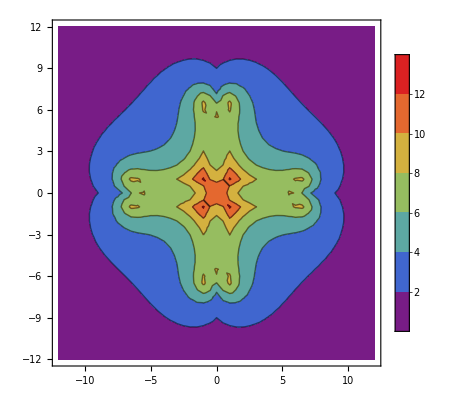

```mathematica
ListContourPlot[ptsPasso,PlotLegends->Automatic,ColorFunction->"Rainbow",AspectRatio->Automatic]
```

## Tensão de Toque

Coeficiente de transmisão

```mathematica
T=2sjweSolo/(sjweAr+sjweSolo)
```

2.-1.11274×10^-19 ⅈ

Diferença de potencial de 1.7 m acima do solo ao solo.

```mathematica
tensaoToque=ParallelTable[
Block[{u,z,pot},
z=1.7;
u=CalcularPotencial[Join[p,{z}],eletrodos,it,γ,sjweSolo,T];
pot=CalcularPotencial[Join[p,{0}],eletrodos,it,γ,sjweSolo,1];
pot+=CalcularPotencial[Join[p,{0}],imagens,it,γ,sjweSolo,R];
Abs[u-pot]
] 
,{p,pontos2d}
];//AbsoluteTiming
```

{1.89056,Null}

```mathematica
tensaoToque//Max
tensaoToque//Min
```

27.5848

0.119401

```mathematica
ptsToque=Table[{pontos2d[[i,1]],pontos2d[[i,2]],tensaoToque[[i]]},{i,pontos2d//Length}];
```

```mathematica
ListPlot3D[ptsToque,PlotRange->All,Mesh->35,ColorFunction->"Rainbow",Boxed->True,Axes->False,PlotLegends->Automatic]
```

-Graphics3D-

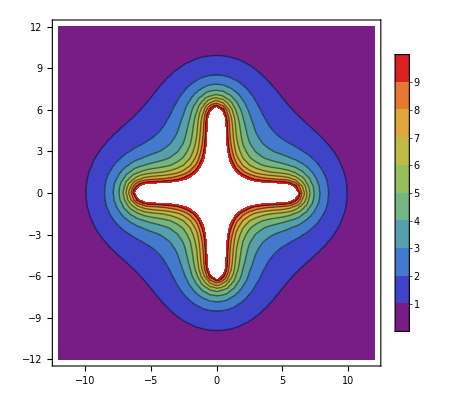

```mathematica
ListContourPlot[ptsToque,PlotLegends->Automatic,ColorFunction->"Rainbow",AspectRatio->Automatic,Contours->Automatic]
```